# nearest neighbor algorithm

## входные данные

### поле:

```mathematica
rows=40;
columns=60;
```

### дроны:

```mathematica
numberOfDrones=4;
turnsOfDrones=10000;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=3;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=7000;
```

### склады:

```mathematica
numberOfWarehouses = 3;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehousesCoords[rows,columns,numberOfWarehouses]
```

{{9,31},{43,37},{13,21}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}]
```

{{3804,116,5753},{2868,3842,2858},{5794,3567,4944}}

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{12466,7525,13555}

### заказы:

```mathematica
numberOfOrders =50;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords];
```

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

223

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
({1}~Join~ConstantArray[0,numberOfProducts-1])+#&/@RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],3],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts];
```

### база данных:

```mathematica
data=<|
"general"-> <|
"rows"->rows,
"columns"->columns,
"turns"-> turnsOfDrones,
"capacity"-> capacityOfDrones,
"numberOfDrones"->numberOfDrones,
"numberOfProducts"->numberOfProducts,
"numberOfWarehouses"-> numberOfWarehouses,
"numberOfOrders"-> numberOfOrders,
"weightsOfProducts"->productsWeights
|>,

"drones"->AssociationThread[Range@numberOfDrones->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧,"score"->#⟦3⟧|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])]~Join~
<|"mask"-> ConstantArray[False,numberOfDrones]|>,

"warehouses"->AssociationThread[Range@numberOfWarehouses->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])],

"orders"-><|
"order"->AssociationThread[Range@numberOfOrders->(<|"coords"->#⟦1⟧,"list"->#⟦2⟧,"turns"-> 0|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders],
"done"->False
|>
|>;
```

```mathematica
data;
```

```mathematica
data["drones"]
```

<|1→<|coords→{9,31},products→{0,0,0},score→0|>,2→<|coords→{9,31},products→{0,0,0},score→0|>,3→<|coords→{9,31},products→{0,0,0},score→0|>,4→<|coords→{9,31},products→{0,0,0},score→0|>,mask→{False,False,False,False}|>

## анализ данных

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses",All,"coords"⟧,Range@data["general","numberOfWarehouses"]}],MapThread[Labeled,{Values@data⟦"orders","order",All,"coords"⟧,
Range@data["general","numberOfOrders"]}]},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}];
```

## алгоритм

на каждой итерации параллельно посылаем дронов на заказы (несколько дронов могут выбрать один заказ и закрыть его за один ход), при этом бронируя продукты.

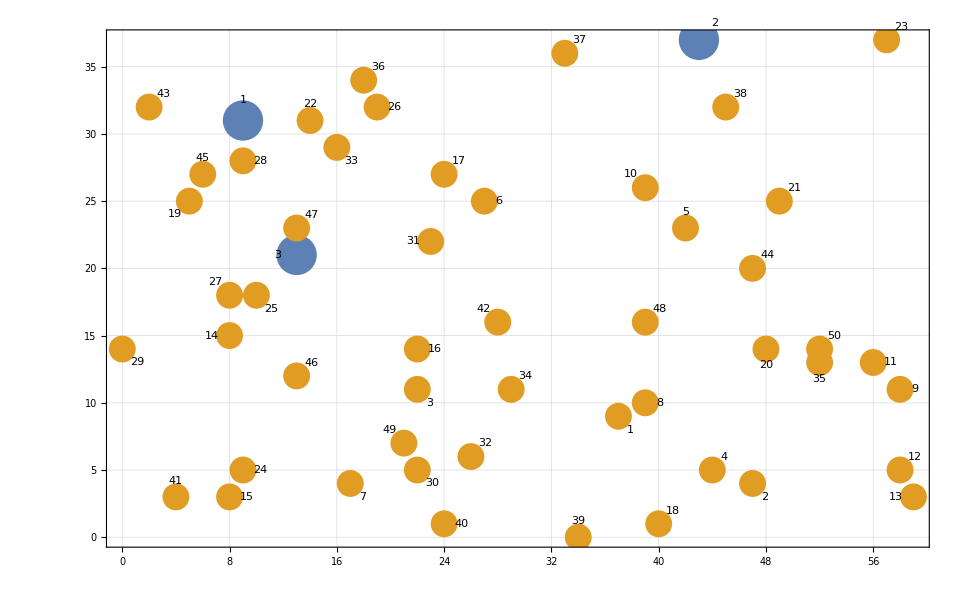

```mathematica
plot
```

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["general","capacity"],weights=data["general","weightsOfProducts"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

(*If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];*)

If[capacity≤0,
Break[]
]

,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@calculateTurns
calculateTurns[turn_Integer,data_Association]:=
With[{T=data["general","turns"]},Ceiling[(T-turn)/T 100]]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones",droneID,"products"⟧;
tempData⟦"drones",droneID,"products"⟧=ConstantArray[0,data["general","numberOfProducts"]];

If[Total@tempData⟦"orders","order",orderID,"list"⟧==0,
tempData⟦"orders","mask",orderID⟧=1;
tempData["orders","order",orderID,"turns"]=calculateTurns[tempData["drones",droneID,"score"],tempData];
If[Total@tempData⟦"orders","mask"⟧==tempData["general","numberOfOrders"],tempData["orders","done"]=True]
(*Print["заказ ",orderID, " полностью выполнен"]*)
];
tempData
]
```

```mathematica
Clear@chooseNextDirection
chooseNextDirection[droneID_,data_Association]:=
Module[
{warehouses,warehouse,order={},warehouseCoords,orderID,orderCoords,tempData=data,score},

If[
!(tempData⟦"drones","mask",droneID⟧∨tempData["orders","done"]),
(*выбор ближайшего склада, где есть хотя бы один продукт*)
warehouses=SortBy[
Normal@
Select[
tempData⟦"warehouses"⟧,
Total@#["products"]≠0&
]⟦All,"coords"⟧,
Ceiling@EuclideanDistance[Last@#,data["drones",droneID,"coords"]]&];

If[warehouses=={},Print["ass"]];
(*определяем ближайший заказ*)
Do[
order=First[
SortBy[
Normal@Select[
Pick[data⟦"orders","order",All⟧,data["orders","mask"],0],Composition[Greater[#,0]&,Total,Times[tempData["warehouses",warehouseLocal⟦1⟧,"products"],#["list"]]&]
]⟦All,"coords"⟧
,
Ceiling@EuclideanDistance[warehouseLocal⟦2⟧,Last@#]&],
{}];
If[order=!={},
warehouse=warehouseLocal;
Break[]],
{warehouseLocal,warehouses}];

warehouseCoords=warehouse⟦2⟧;
orderID=order⟦1⟧;
orderCoords=order⟦2⟧;

(*"бронируем" продукты, то есть сразу же загружаем*)
score=Ceiling@EuclideanDistance[data["drones",droneID,"coords"],warehouseCoords]+Ceiling@EuclideanDistance[warehouseCoords,orderCoords];
If[
tempData["drones",droneID,"score"]+score≥tempData["general","turns"],
tempData⟦"drones","mask",droneID⟧=True;
Return[tempData]
];

tempData=loadProducts[tempData,warehouse⟦1⟧,orderID,droneID];

tempData["drones",droneID,"coords"]=orderCoords;
tempData["drones",droneID,"score"]+=score;
If[
tempData["drones",droneID,"score"]>data["general","turns"],
Print["превышено количество ходов"];
Abort[]
];

(*разгружаем*)
unloadProduct[tempData,orderID,droneID],
tempData
]
]
```

```mathematica
data["orders","done"]
```

False

```mathematica
Clear@solve
solve[data_Association]:=
Module[
{tempData=data},
If[!And@@Positive[Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@data⟦"orders","order",All,"list"⟧],
Print["недостаточно продуктов на складах"];Return[{}]
];
While[
!tempData["orders","done"],
If[
And@@tempData["drones","mask"],
Print["не хватило ходов"];
Return[tempData]
];
Do[
tempData=chooseNextDirection[i,tempData]
,{i,tempData["general","numberOfDrones"]}
]
];
tempData
]
```

```mathematica
solution=solve[data];//AbsoluteTiming
```

{0.346684,Null}

```mathematica
solution["drones","mask"]
```

{False,False,False,False}

```mathematica
And@@Positive[Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@data⟦"orders","order",All,"list"⟧]
```

True

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧==(Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@solution⟦"warehouses",All,"products"⟧)
```

True

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧
```

{120,87,66}

```mathematica
Values@solution⟦"warehouses",All,"products"⟧
```

{{3781,101,5743},{2823,3817,2827},{5742,3520,4919}}

```mathematica
SortBy[solution⟦"orders","order",All,"turns"⟧,Value]
```

<|13→83,12→84,2→85,9→85,4→86,18→87,39→87,1→88,11→88,8→89,20→90,35→90,50→90,48→91,5→92,23→92,44→92,10→93,21→93,37→93,38→93,40→93,32→94,34→94,41→94,7→95,15→95,30→95,49→95,24→96,42→96,3→97,6→97,29→97,17→98,26→98,36→98,14→99,16→99,27→99,31→99,46→99,19→100,22→100,25→100,28→100,33→100,43→100,45→100,47→100|>